## Generalized Evidence Lower Bound (ELBO) using Coupled Entropy

The purpose of this notebook is derive the generalization of the Evidence Lower Bound (ELBO), also known as the Variational Lower Bound, using two forms of the Coupled Entropy, with and without a root term for the coupled logarithm. Furthermore, the notebook will show that the ELBO can be translated into the probability domain, so that the ELBO for an individual sample is the same for all generalizations, while the averages correspond to different generalized means of the individuals.

### ELBO or Variational Bound using Shannon Entropy

From (Kingma, Welling, 2014 and (Kingma, Welling, 2019) we have the following derivation and justification for the ELBO or Variational Bound.

#### Generalized ELBO with Coupled Entropy

ℒ(θ,ϕ;κ,α,d;x^(i))= - D_κ(q_ϕ^(α/(1+d κ))(z|x^(i))||p_θ^(α/(1+d κ))(z)) + 𝔼_(q_ϕ^(α,d,κ)(z|x^(i)))[log_κ p_θ^(α/(1+d κ))(x^(i)|z)]
				= -1/(2κ)∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(α κ)/(1+d κ))((q_ϕ(z|x^(i)))^((-α κ)/(1+d κ))-(p_θ(z))^((-α κ)/(1+d κ)))ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(α κ)/(1+d κ))ⅆz+-1/(2κ)∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(α κ)/(1+d κ))((p_θ(x^(i)|z))^((-α κ)/(1+d κ))-1)ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(α κ)/(1+d κ))ⅆz

Care is needed with the negative signs in this expression for the ELBO. In particular the relationship  log_(κ,α,d)p(x) = 1/(α κ)((p(x))^((α κ)/(1+d κ))-1)=  -1/(α κ)( (p(x))^((-α κ)/(1+d κ))-1). The cross-entropy expression from which the coupled entropy and coupled divergence can be derived has the form 
H_(κ,α,d)(p,q) =-𝔼_(p,κ,α,d)[log_(κ,α,d)q]=𝔼_(p,κ,α,d)[log_(κ,α,d)q^-1]. To facilitate further analysis the expressions for the generalized ELBO were written so that -1/(2κ)is the multiple for both terms and the probabilities are raised to the power (-α κ)/(1 + d κ). The generalized ELBO is going to be optimized for different values of κ with α = 2.

### Risk Assessment - Coupled ELBO in Probability Domain

To facilitate a comparison across κ, the single sample expression can be translated to the probability domain by applying the inverse of the coupled logarithm expression.
Given x=1/(α κ)( y^((α κ)/(1+d κ))-1), the inverse is then y=(1+α κ x)^((1+d κ)/(α κ)), which is expressed as
(exp_κ(α x))^((1+d κ)/α). Completing this translation to the probability domain and substituting for α = 2 and d = 1 gives the following expressions. Note that in the probability domain the coupled divergence and the coupled log-likelihood are combined using the coupled product.
(exp_κ(2ℒ(θ,ϕ;κ,2,1;x^(i))))^((1+d κ)/-2)=
(exp_κ(-2D_κ(q_ϕ^(2/(1+d κ))(z|x^(i))||p_θ^(2/(1+d κ))(z)) + 2𝔼_(q_ϕ^(2,d,κ)(z|x^(i)))[log_κ p_θ^(2/(1+d κ))(x^(i)|z)]))^((1+ d κ)/-2)=( (exp_κ(-2D_κ(q_ϕ^(2/(1+d κ))(z|x^(i))||p_θ^(2/(1+d κ))(z)) ⊗_κ exp_κ(2𝔼_(q_ϕ^(2,d,κ)(z|x^(i)))[log_κ p_θ^(2/(1+d κ))(x^(i)|z)])))^((1+ d κ)/-2)=(1+2κ(-1/(2κ)∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+ d κ))((q_ϕ(z|x^(i)))^((-2 κ)/(1+d κ))-(p_θ(z))^((-2 κ)/(1+d κ)))ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))ⅆz+-1/(2κ)∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))((p_θ(x^(i)|z))^((-2 κ)/(1+d κ))-1)ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))ⅆz))^((1+ 2 κ)/(-2 κ))
=(1-∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))((q_ϕ(z|x^(i)))^((-2 κ)/(1+d κ))-(p_θ(z))^((-2 κ)/(1+d κ)))ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))ⅆz-∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))((p_θ(x^(i)|z))^((-2 κ)/(1+d κ))-1)ⅆz/∫_(z∈ℝ^d) (q_ϕ(z|x^(i)))^(1+(2 κ)/(1+d κ))ⅆz))^((1+ d κ)/(-2 κ))

#### Source of Difficulty in Developing Graphical Visualization of the Coupled ELBO and its components

Plan to replace this section with a clear explanation of the visulalization including:
1) The histograms of the divergence and log-likelihood terms are shown together
2) Overlaying the two histograms are the Coupled ELBO Probability metrics, which combine the metrics of the two histograms using the coupled product.

In order to develop a graphical visualization of the Coupled ELBO and its components, each of the components and the combination need to be representable in the form of a probability and the combination needs to be defined independent of the coupling. However, these requirements depend on how the Coupled ELBO is defined and the current formulation does not lend itself to this construction. The reason is that each component of the ELBO was generalized and then added together; however, these means that alternative construction in which the coupled logarithm is applied to a combination of the component probabilities requires  that the probabilities be combined using the coupled sum. Worse this problem also affects the Coupled Divergence by itself since the coupled logarithm is applied to each distribution and then the result is substracted. 

To illustrate the problem mathematically two different approaches to defining the negative ELBO are shown. For simplification the parameters are set to α = 1 and 
d = 0, so that only the coupling parameter is considered. The current definition of the negative Coupled ELBO loss is
ℒ(θ,ϕ;κ,1,0;x^(i))≡-D_κ(q_ϕ^□(z|x^(i))||p_θ^□(z)) + 𝔼_(q_ϕ^(α,d,κ)(z|x^(i)))[log_κ p_θ^□(x^(i)|z)]
= ∑_(j=1)^n_z q_ϕ^□(z_j|x^(i))(ln_κ q_ϕ^□(z_j|x^(i))-ln_κ p_θ^□(z_j)+ln_κ p_θ^□(x^(i)|z_j))
= ∑_(j=1)^n_z q_ϕ^□(z_j|x^(i))(ln_κ(q_ϕ^□(z_j|x^(i))⊙_k p_θ^□(z_j)⊗_κ p_θ^□(x^(i)|z_j))
where the coupled product ⊗_κ, coupled division ⊙_kare defined according to the methods of E. P. Borges, “A possible deformed algebra and calculus inspired in nonextensive thermostatistics,” Phys. A Stat. Mech. its Appl., vol. 340, no. 1–3, pp. 95–101, 2004.
	a ⊗_κ b ≡ (a^κ + (b^κ-1))^(1/κ) ; a ⊙_κ b ≡ (a^κ - (b^κ+1))^(1/κ)

The difficulty is that the combination of the individual probabilities involves the generalization. In contrast if the negative ELBO were defined treating the combination of probabilities as independent and thus using standard multiplication and division then the function would be	
ℒ^I(θ,ϕ;κ,1,0;x^(i))≡∑_(j=1)^n_z q_ϕ^□(z_j|x^(i))(ln_κ((q_ϕ^□(z_j|x^(i))p_θ^□(x^(i)|z_j))/(p_θ^□(z_j))))
=∑_(j=1)^n_z q_ϕ^□(z_j|x^(i))[ln_κ q_ϕ^□(z_j|x^(i))⊕_κ ln_κ p_θ^□(x^(i)|z_j)⊖_κ ln_κ p_θ^□(z_j)] 
	coupled sum ⊕_κ and the coupled difference ⊖_κ 
	a ⊕_κ b ≡ a + b + κab; a ⊖_κ b ≡ (a - b)/(1+κb)

#### Derivation of the Coupled Algebra Relationships

ln_κ a⊗_κ b≡ln_κ a+ln_κ b
1/κ((a^κ+b^κ-1)^(1/κ))^κ-1)=1/κ(a^κ-1)+1/κ(b^κ-1)
                              1/κ(a^κ+b^κ-2)=1/κ(a^κ+b^κ-2)
ln_κ a⊙_κ b≡ln_κ a-ln_κ b
1/κ((a^κ-b^κ+1)^(1/κ))^κ-1)=1/κ(a^κ-1)-1/κ(b^κ-1)
                                      1/κ(a^κ-b^κ)=1/κ(a^κ-b^κ)
        ln_κ ab≡ln_κ a ⊕_κ ln_κ b
            1/κ((ab)^κ-1) = 1/κ(a^κ-1)+1/κ(b^κ-1) + κ 1/κ(a^κ-1)1/κ(b^κ-1)
            1/κ(a^κ b^κ-1) = 1/κ(a^κ+b^κ+a^κ b^κ-a^κ-b^κ-2+1)
            1/κ(a^κ b^κ-1) =1/κ(a^κ b^κ-1) 
       ln_κ a/b≡ln_κ a ⊖_κ ln_κ b
              1/κ((a/b)^κ-1) = (1/κ(a^κ-1)-1/κ(b^κ-1))/(1+κ 1/κ(b^κ-1))
             1/κ(a^κ b^-κ-1) =(1/κ(a^κ-b^κ))/b^κ= 1/κ(a^κ b^-κ-1)

#### Attempt at Simplification - Upon further examination this does not work

Since this translation has some difficulties first examine the case with κ = 0
Exp[ℒ(θ,ϕ;0,2,1;x^(i))]=Exp[-D(q_ϕ(z|x^(i))||p_θ(z)) + 𝔼_(q_ϕ(z|x^(i)))[log p_θ(x^(i)|z)]]
			=Exp[-D(q_ϕ(z|x^(i))||p_θ(z)) ]Exp[𝔼_(q_ϕ(z|x^(i)))[log_ p_θ(x^(i)|z)]]]

While this could be expressed as a product of two geometric means in continuous domain or equivalently log-averages, its not clear that a) this further simplifies and b) that the same expression would be achieved for different values of the κ. While each data sample x^(i)is being considered individually, there are still full distributions of q and p under examination.

Putting aside the expectation over q_ϕ(z|x^(i))for each term, the expression can be arranged as
Exp[log (p_θ(z)/q_ϕ(z|x^(i))) ]Exp[log p_θ(x^(i)|z)]] = (p_θ(z)p_θ(x^(i)|z))/(q_ϕ(z|x^(i)))=((p_θ(z))/(q_ϕ(z|x^(i))))p_θ(x^(i)|z)
p_θ(x^(i)|z): I believe this probability is what we plotted for our evaluation
Replacing the expectation but as a power, the integral is 
Exp[∫_(-∞)^∞ (Log((p_θ(z)p_θ(x^(i)|z))/(q_ϕ(z|x^(i)))))^(q_ϕ(z|x^(i)))ⅆz]
Examining each component
Exp[∫_(-∞)^∞ (Log(1/(q_ϕ(z|x^(i)))))^(q_ϕ(z|x^(i)))ⅆz]: Density average (entropy in density domain) of the latent distribution given a sample x^(i)
Exp[∫_(-∞)^∞ (Log(p_θ(z)))^(q_ϕ(z|x^(i)))ⅆz]: Inverse cross density average of the prior latent distribution over the latent distribution given a sample x^(i)
Exp[∫_(-∞)^∞ (Log(p_θ(x^(i)|z)))^(q_ϕ(z|x^(i)))ⅆz]: Inverse cross density average of the sample given the latent variable over the latent distribution given a sample x^(i)

If this expression can be computed for each sample, then there is the possibility of also computing the respective averages for different values of κ. The relevant values of κ would be a) those that form the -2/3rd, zero, and 1 geometric means and b) the average formed by the value of κ which was used for the optimization.

```mathematica
Subscript[Exp, κ][Subscript[log, κ] (Subscript[p, θ](z)/Subscript[q, ϕ](z|x^(i))) ]Subscript[Exp, κ][Subscript[log, κ] Subscript[p, θ](x^(i)|z)]] = (Subscript[p, θ](z)Subscript[p, θ](x^(i)|z))/(Subscript[q, ϕ](z|x^(i)))=((Subscript[p, θ](z))/(Subscript[q, ϕ](z|x^(i))))Subscript[p, θ](x^(i)|z)
```

```mathematica
[Subscript[log, κ] (Subscript[p, θ](z)/Subscript[q, ϕ](z|x^(i))) ]+_κ[Subscript[log, κ] Subscript[p, θ](x^(i)|z)]]
```

## Examination of Divergence with Standard Gaussian

```mathematica
Manipulate[Plot[
{PDF[NormalDistribution[0,σ],x],PDF[NormalDistribution[],x],
Exp[∫_(-∞)^∞ PDF[NormalDistribution[0,σ],y]Log[PDF[NormalDistribution[],y]/PDF[NormalDistribution[0,σ],y]]ⅆy]},
{x,-5,5},
PlotTheme->"Scientific",
FrameLabel->{"x","PDF"},
PlotRange->{{-5,5},{0,5}}
],
{{σ,0.5},0.05,2}
]
```

```mathematica
Log[1]
```

0

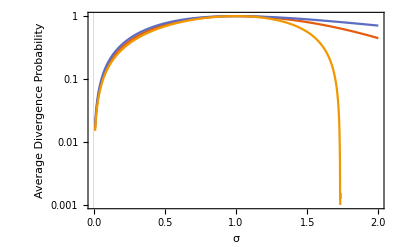

```mathematica
LogPlot[{
Exp[∫_(-∞)^∞ PDF[NormalDistribution[0,σ],y]Log[PDF[NormalDistribution[],y]/PDF[NormalDistribution[0,σ],y]]ⅆy],
CoupledExponential[∫_(-∞)^∞ PDF[NormalDistribution[0,σ],y]
CoupledLogarithm[PDF[NormalDistribution[],y]/PDF[NormalDistribution[0,σ],y],(-(-2/3))/((-2/3)+2),1]ⅆy,
(-(-2/3))/((-2/3)+2),1],
CoupledExponential[∫_(-∞)^∞ PDF[NormalDistribution[0,σ],y]
CoupledLogarithm[PDF[NormalDistribution[],y]/PDF[NormalDistribution[0,σ],y],(-(1))/((1)+2),1]ⅆy,
(-(1))/((1)+2),1]
},
{σ,0.01,2},
PlotTheme->"Scientific",
FrameLabel->{"σ","Average Divergence Probability"},
PlotRange->{{0,2},{10^-3,1}}
]
```

#### Saved Results

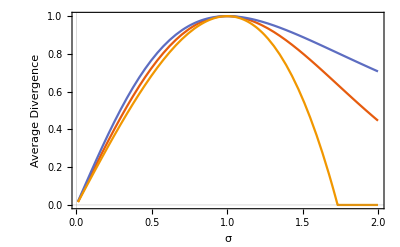

-Graphics-